```mathematica
qA = ⅈ L/2;
M1={{1,L/2},{0,1}};
```

```mathematica
f2 =(-L/2)/(n2-1);
M2={{1,0},{-1/f2,1}};
```

```mathematica
M3={{1,z3},{0,1}};
M3={{1,0},{-1/f3,1}}.M3;
(*第二个透镜 f3. z3 是从第二个透镜到第一个腔镜*)
```

```mathematica
M4={{1,z4-z3},{0,1}};
M4={{1,0},{-1/f4,1}}.M4;
(*第一个透镜 f4. z4 是从第一个透镜到第一个腔镜*)
```

```mathematica
M=M4.M3.M2.M1;
```

```mathematica
q0=Simplify[(qA M[[1,1]]+M[[1,2]])/(qA M[[2,1]]+M[[2,2]])];
```

```mathematica
q00=(π 0.52^2)/(370*10^-6);
L=300;
n2=1.48;(*忽略第一个腔镜的折射作用*)
Z=2000.0;(*从激光束腰到第一个腔镜*)
f3=75.0;
f4=100.0;
Element[z3,Reals];
Element[z4,Reals];
Element[z5,Reals];
Element[z6,Reals];
```

```mathematica
FindRoot[{Refine[Re[ComplexExpand[q0]],z4>z3>0]==0,Refine[Im[ComplexExpand[q0]],z4>z3>0]==q00},{{z3,10},{z4,160}}]
```

{z3→229.839,z4→424.034}

```mathematica
(z4-z3)/.%88
```

194.195

```mathematica
(*需要提高z3鲁棒性*)
```

```mathematica
Clear[L,n2,Z,f3,f4]
```

```mathematica
M5={{1,z5-z4},{0,1}};
M5={{1,0},{-1/f3,1}}.M5;
```

```mathematica
M6={{1,z6-z5},{0,1}};
M6={{1,0},{-1/f3,1}}.M6;
```

```mathematica
M7={{1,Z-z6},{0,1}};
```

```mathematica
M=M7.M6.M5.M4.M3.M2.M1;
```

```mathematica
q0=Simplify[(qA M[[1,1]]+M[[1,2]])/(qA M[[2,1]]+M[[2,2]])];
```

```mathematica
q00=(π 0.52^2)/(370*10^-6);
L=300;
n2=1;(*忽略第一个腔镜的折射作用*)
Z=2000.0;(*从激光束腰到第一个腔镜*)
f3=200.0;
f4=100.0;
Element[z3,Reals];
Element[z4,Reals];
Element[z5,Reals];
Element[z6,Reals];
```

```mathematica
FindRoot[{Refine[Re[ComplexExpand[q0]],z6>z5>z4>z3>0]==0,Refine[Im[ComplexExpand[q0]],z6>z5>z4>z3>0]==q00,Refine[Re[ComplexExpand[D[q0,z3]]],z6>z5>z4>z3>0]==0,Refine[Im[ComplexExpand[D[q0,z3]]],z6>z5>z4>z3>0]==0},{{z3,500},{z4,1000},{z5,1500},{z6,1800}}]
```

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到 merit 函数的充足的降低. 您可能需要多于 MachinePrecision 位工作精度以满足这些容差.

{z3→574.173,z4→1092.32,z5→1436.13,z6→1765.42}

```mathematica
qA = ⅈ L/2;
M1={{1,L/2},{0,1}};
```

```mathematica
(*f2 =(-L/2)/(n2-1);
M2={{1,0},{-1/f2,1}};*)
```

```mathematica
M3={{1,z3},{0,1}};
M3={{1,0},{-1/f3,1}}.M3;
(*第二个透镜 f3. z3 是从第二个透镜到第一个腔镜*)
```

```mathematica
M4={{1,z4-z3},{0,1}};
M4={{1,0},{-1/f4,1}}.M4;
(*第一个透镜 f4. z4 是从第一个透镜到第一个腔镜*)
```

```mathematica
M=M4.M3.M1;
```

```mathematica
q0=Simplify[(qA M[[1,1]]+M[[1,2]])/(qA M[[2,1]]+M[[2,2]])];
```

```mathematica
q00=(π 0.52^2)/(370*10^-6);
L=300;
Z=2000.0;(*从激光束腰到第一个腔镜*)
f3=50.0;
f4=100.0;
Element[z3,Reals];
Element[z4,Reals];
Element[z5,Reals];
Element[z6,Reals];
```

```mathematica
FindRoot[{Refine[Re[ComplexExpand[q0]],z4>z3>0]==0,Refine[Im[ComplexExpand[q0]],z4>z3>0]==q00},{{z3,200},{z4,350}}]
```

{z3→152.507,z4→309.636}

```mathematica
qA = ⅈ L/2;
M1={{1,L/2},{0,1}};
```

```mathematica
(*f2 =(-L/2)/(n2-1);
M2={{1,0},{-1/f2,1}};*)
```

```mathematica
M3={{1,z3},{0,1}};
M3={{1,0},{-1/f3,1}}.M3;
(*第二个透镜 f3. z3 是从第二个透镜到第一个腔镜*)
```

```mathematica
M4={{1,z4-z3},{0,1}};
M4={{1,0},{-1/f4,1}}.M4;
(*第一个透镜 f4. z4 是从第一个透镜到第一个腔镜*)
```

```mathematica
M=M4.M3.M1;
```

```mathematica
q0=Simplify[(qA M[[1,1]]+M[[1,2]])/(qA M[[2,1]]+M[[2,2]])];
```

```mathematica
q00=(π 0.52^2)/(638*10^-6);
L=300;
Z=4000.0;(*从激光束腰到第一个腔镜*)
f3=100.0;
f4=200.0;
Element[z3,Reals];
Element[z4,Reals];
Element[z5,Reals];
Element[z6,Reals];
```

```mathematica
FindRoot[{Refine[Re[ComplexExpand[q0]],z4>z3>0]==0,Refine[Im[ComplexExpand[q0]],z4>z3>0]==q00},{{z3,100},{z4,400}}]
```

{z3→118.989,z4→447.674}

```mathematica
(*光纤出来准直一下再进PDH*)
```

```mathematica
qfiber = (ⅈ π *0.0024^2)/(370*10^-6);
fcollimat=4;
qfiber = qfiber+fcollimat;
Mcollimat = {{1,0},{-1/fcollimat,1}};
```

```mathematica
qe = (qfiber Mcollimat[[1,1]]+Mcollimat[[1,2]])/(qfiber Mcollimat[[2,1]]+Mcollimat[[2,2]])
```

-4.+327.152 ⅈ

```mathematica
Clear[L,f3,f4]
```

```mathematica
qA = ⅈ L/2;
M1={{1,L/2},{0,1}};
```

```mathematica
n2 = 1.474;
d2 = 3.27;
M2={{1,d2/n2},{0,1}};
```

```mathematica
M3={{1,z3},{0,1}};
M3={{1,0},{-1/f3,1}}.M3;
(*第二个透镜 f3. z3 是从第二个透镜到第一个腔镜*)
```

```mathematica
M4={{1,z4-z3},{0,1}};
M4={{1,0},{-1/f4,1}}.M4;
(*第一个透镜 f4. z4 是从第一个透镜到第一个腔镜*)
```

```mathematica
M=M4.M3.M2.M1;
```

```mathematica
q0=Simplify[(qA M[[1,1]]+M[[1,2]])/(qA M[[2,1]]+M[[2,2]])];
```

```mathematica
L=301;
Z=4000.0;(*从光纤准直透镜到第一个腔镜*)
f3=150.0;
f4=150.0;
Element[z3,Reals];
Element[z4,Reals];
Element[z5,Reals];
Element[z6,Reals];
```

```mathematica
FindRoot[{Refine[Re[ComplexExpand[q0]],z4>z3>0]==Re[qe],Refine[Im[ComplexExpand[q0]],z4>z3>0]==Im[qe]},{{z3,190},{z4,500}}]
```

{z3→188.049,z4→535.152}

```mathematica
(z3/.%155)-(z3/.%146)
```

-0.379648

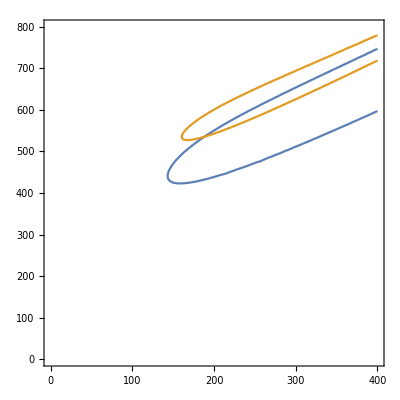

```mathematica
ContourPlot[{Refine[Re[ComplexExpand[q0]],z4>z3>0]==Re[qe],Refine[Im[ComplexExpand[q0]],z4>z3>0]==Im[qe]},{z3,0,400},{z4,0,800}]
```

```mathematica
4.9048+0.11768/(λ^2-0.0475)-0.027169 λ^2/.{λ->370*10^-6}
```

2.42732

```mathematica
(*铌酸锂对370的折射率*)
```

```mathematica
w0 = 0.018;
λ = 369.5*10^-6;
Ω0 = w0^2 π/λ;
Z=870;
```

```mathematica
f = 500;
sol = NSolve[(f(z1(f-z1)-Ω0^2))/((f-z1)^2+Ω0^2)+z1==Z,z1]
```

{{z1→1597.74},{z1→499.974},{z1→272.287}}

```mathematica
Clear[f,Ω0,Z]
```

```mathematica
D[(f(z1(f-z1)-Ω0^2))/((f-z1)^2+Ω0^2)+z1,z1]
```

```mathematica
1+(2 f (f-z1) ((f-z1) z1-Ω0^2))/(((f-z1)^2+Ω0^2)^2)+(f (f-2 z1))/((f-z1)^2+Ω0^2)
```

```mathematica
Simplify[1/%]
```

1/(1+(2 f (f-z1) ((f-z1) z1-Ω0^2))/(((f-z1)^2+Ω0^2)^2)+(f (f-2 z1))/((f-z1)^2+Ω0^2))

```mathematica
%16/.sol[[3]]
```

5.81919

```mathematica
{(f^2 Ω0)/((f-z1)^2+Ω0^2),√(λ/π(f^2 Ω0)/((f-z1)^2+Ω0^2))}/.sol[[3]]
```

{13.2795,0.0395206}